```mathematica
(*Code created by Loïc Marrec*)
```

```mathematica
(*Description:Mean number of dispersal events*)
```

```mathematica
(*PARAMETERS*)
```

```mathematica
bW=1;(*Wild-type birth rate*)
```

```mathematica
dW=0.1;(*Wild-type death rate*)
```

```mathematica
bM=Table[i,{i,0.95,1.1,0.001}];(*Mutant birth rates*)
```

```mathematica
dM=0.1;(*Mutant death rate*)
```

```mathematica
Δ=5;(*Number of demes*)
```

```mathematica
Ν=100;(*Carrying capacity*)
```

```mathematica
(*EQUILIBRIUM DEME SIZES*)
```

```mathematica
NW=Ν*(1-dW/bW);(*Wild-type equilibrium size*)
```

```mathematica
NM=Table[Ν*(1-dM/bM[[i]]),{i,1,Length[bM]}];(*Mutant equilibrium sizes*)
```

```mathematica
(*FIXATION PROBABILITIES WITHIN DEMES*)
```

```mathematica
uW=Table[If[bM[[i]]==bW*dM/dW,1/NM[[i]],(1-(bM[[i]]*dW)/(bW*dM))/(1-((bM[[i]]*dW)/(bW*dM))^NM[[i]])],{i,1,Length[bM]}];(*Fixation probability of a wild-type in a mutant deme*)
```

```mathematica
uM=Table[If[bM[[i]]==bW*dM/dW,1/NW,(1-(bW*dM)/(bM[[i]]*dW))/(1-((bW*dM)/(bM[[i]]*dW))^NW)],{i,1,Length[bM]}];(*Fixation probability of a mutant in a wild-type deme*)
```

```mathematica
(*DISPERSAL RATIOS*)
```

```mathematica
α={1/5,1/2,1,2,5};
```

```mathematica
(*RELATIVE FITNESS OF MUTANT DEMES*)
```

```mathematica
r=Table[α[[j]]*(NM[[i]]*uM[[i]])/(NW*uW[[i]]),{i,1,Length[bM]},{j,1,Length[α]}];
```

```mathematica
r0=Table[α[[j]]*NM[[i]]/NW,{i,1,Length[bM]},{j,1,Length[α]}];
```

```mathematica
(*NUMBER OF DISPERSAL EVENTS*)
```

```mathematica
n=Table[If[r[[i]][[j]]==1,((Δ^2-1)*(1+r0[[i]][[j]]))/(6*r0[[i]][[j]]*uM[[i]]),(((1+r[[i]][[j]]^-Δ)*(-1+r[[i]][[j]]^-1)-(1/Δ)*(-1+r[[i]][[j]]^-Δ)*(1+r[[i]][[j]]^-1))*(1+r0[[i]][[j]]^-1)*Δ)/(uM[[i]]*(-1+r[[i]][[j]]^-1)*(-1+r[[i]][[j]]^-Δ)*(-1+r[[i]][[j]]^-1))],{i,Length[bM]},{j,1,Length[α]}];
```

```mathematica
(*DATA PREPARATION AND VISUALIZATION*)
```

```mathematica
ntable=Table[{bM[[j]]/bW-1,n[[j]][[i]]},{i,1,Length[α]},{j,1,Length[bM]}]; (*Selection coefficient vs.number of dispersal events*)
```

```mathematica
colorRain=Table[ColorData["Rainbow"][k],{k,0,1,1/(Length[α]-1)}];(*Color scheme*)
```

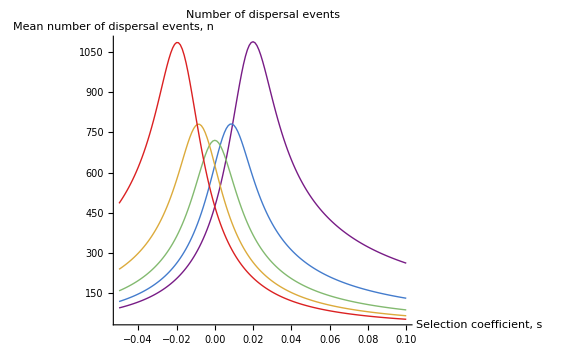

```mathematica
Show[Table[ListPlot[ntable[[f]],PlotStyle->{colorRain[[f]],Thick},Joined->True],{f,1,Length[α]}],PlotLabel->"Number of dispersal events",PlotRange->All,AxesLabel->{"Selection coefficient, s","Mean number of dispersal events, n"},ImageSize->Large]
```